# Benchmark amplitude implementations

## Loading resources

### Packages

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/AmplitudeSubtractionBenchmark

All expressions in this notebook match the conventions of Package X, as given in[arXiv : 1612.00009] .

```mathematica
Get["./packageX/X/Kernel/init.m"]
```

Package-X v2.1.1 already initialized
For more information, see the

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/cLTD.m"]
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→FORMPATH
tFORMpath→tform
WorkingDirectory→/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/AmplitudeSubtractionBenchmark/cLTD_work_dir/
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

### Zenos tooling

```mathematica
SP[v_,w_]:=v[[1]]w[[1]]-v[[2]]w[[2]]-v[[3]]w[[3]]-v[[4]]w[[4]]
```

```mathematica
norm3D[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]
```

```mathematica
vec[w_]:={w[[2]],w[[3]],w[[4]]}
```

```mathematica
ClearAll[p1,p2,p3,p4]
```

```mathematica
esurf[k_,p1_,p2_]:=norm3D[k+vec[p1]]+norm3D[k+vec[p2]]-p2[[1]]+p1[[1]];
```

```mathematica
zerovec={0,0,0,0};
```

```mathematica
GetKinematics[p11_,p22_,p33_]:=Module[
{SP11,SP22,SP33,ps},
If[
p11<0 &&p22<0&&p33<0,
SP11=-p11;
SP22=-p22;
SP33=-p33;
{
{0,(√(-SP11^2-(SP22-SP33)^2+2 SP11 (SP22+SP33)))/(2 √SP33),0,-(SP11-SP22+SP33)/(2 √SP33)},
{0,-(√(-SP11^2-(SP22-SP33)^2+2 SP11 (SP22+SP33)))/(2 √SP33),0,-(-SP11+SP22+SP33)/(2 √SP33)},
{0,0,0,√SP33}
},
If[
p11>0 &&p22>0&&p33>0,
SP11=p11;
SP22=p22;
SP33=p33;
{
{-(SP11-SP22+SP33)/(2 √SP33),0,0,-(√(SP11^2+(SP22-SP33)^2-2 SP11 (SP22+SP33)))/(2 √SP33)},
{-(-SP11+SP22+SP33)/(2 √SP33),0,0,(√(SP11^2+(SP22-SP33)^2-2 SP11 (SP22+SP33)))/(2 √SP33)},
{√SP33,0,0,0}
}
,
Throw["Kinematics not implemented"]
]
]
]
```

### Integration tooling

```mathematica
rounded[num_,prec_]:=Block[
{res},
res=10^(Ceiling[Log10[num]]-prec);
Floor[(num/res)]*res*1.
]
```

```mathematica
MyPrint[msg_]:=Print[Style[msg,FontFamily->"Monaco"]];
```

```mathematica
MonitoredNIntegrate[NIargs_,OptionsPattern[{TargetRes->Null,StackPrints->False,MonitorInterval->1.,Silence->True}]]:=Module[
{
AllNIargs,
iRegionMethods,
tmpPrint,
allBoundaryRes,
currInt,currErr,
startTime,currTime,
LastUpdateTime,msg,
res,
Npoints,
SpecifiedMaxPoints
},
SpecifiedMaxPoints=(MaxPoints/.Select[NIargs,MatchQ[#,Rule[x_,y_]]&]);
iRegionMethods={"Axis","Boundaries","Dimension","Error","GetRule","Integral","Integrand","WorkingPrecision"};
tmpPrint=Null;
allBoundaryRes=Null;
currInt=0.;
currErr=0.;
startTime=SessionTime[];
currTime=0.;
LastUpdateTime=Null;
Npoints=0;
AllNIargs=Join[NIargs,{
EvaluationMonitor:>Npoints++,
IntegrationMonitor:>Function[{iregs},
currTime=SessionTime[];
If[Or[LastUpdateTime===Null,currTime-LastUpdateTime>OptionValue[MonitorInterval]],
LastUpdateTime=currTime;
allBoundaryRes=Association/@Transpose[Map[Thread[#->Through[iregs[#]]]&,iRegionMethods]];
currInt=Total[Table[cell["Integral"],{cell,allBoundaryRes}]];
currErr=Sqrt[Total[Table[cell["Error"]^2,{cell,allBoundaryRes}]]];
Sow[<|
"t"->Round[currTime-startTime,0.1],"I"->currInt,"Δ"->currErr,"Δ [%]"->Round[Abs[currErr/currInt]*100,0.001], 
"ΔTarget [%]"-> If[OptionValue[TargetRes]===Null,0.,Round[Abs[(currInt-OptionValue[TargetRes])/OptionValue[TargetRes]]*100,0.001]],
"ΔTarget [σ]"-> If[OptionValue[TargetRes]===Null,0.,Round[Abs[(currInt-OptionValue[TargetRes])/currErr],0.1]]
|>];
msg=StringPadRight[ToString[Round[currTime-startTime,0.1]],5]<>"s : "<>StringPadRight[ToString[If[Npoints>1000000,Round[Npoints/1000000.,0.001],Round[Npoints/1000.,0.1]]]<>If[Npoints>1000000,"M evals","K evals"],15]<>
StringPadRight[If[NumberQ[SpecifiedMaxPoints],"( "<>StringPadRight[ToString[Round[Npoints/SpecifiedMaxPoints*100,0.1]]<>"% )",10],""],15]
<>StringPadRight[ToString[FortranForm[currInt]],20]<>" +- "<>StringPadRight[ToString[FortranForm[rounded[currErr,3]]],15]<>" ( "<>StringPadRight[ToString[Round[Abs[currErr/currInt]*100,0.001]]<>"% )",12]<>StringPadRight[If[OptionValue[TargetRes]===Null,"",(" vs target "<>ToString[Round[Abs[(currInt-OptionValue[TargetRes])/OptionValue[TargetRes]]*100,0.001]]<>"%")],20]<>StringPadRight[If[OptionValue[TargetRes]===Null,"",(" ( "<>ToString[Round[Abs[(currInt-OptionValue[TargetRes])/currErr],0.1]]<>"σ )")],10];
If[Not[OptionValue[StackPrints]],
If[Not[tmpPrint===Null],NotebookDelete[tmpPrint]];
tmpPrint=PrintTemporary[msg];
,
MyPrint[msg];
];
]
]
}];
res=Reap[
If[OptionValue[Silence],
Quiet[NIntegrate@@AllNIargs]
,
NIntegrate@@AllNIargs
]
];
{res⟦1⟧,Dataset[res⟦2⟧]}
]
```

### CFF tooling

```mathematica
ClearAll[ConvertCFFFormat];
ConvertCFFFormat[structuredCFF_,g_]:=Module[
{externalEdges,ShiftsReplacement,reducedGraph,flipConfiguration,tmpOrientation,momLabels},
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];

ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}];
momLabels=cFFGenerateMomentaLabels[g];

SortBy[Table[
flipConfiguration=Association[Table[
tmpOrientation=o["Orientation"][Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"]];
e->tmpOrientation,{e,EdgeList[reducedGraph]}]];
{
Association[Table[ok->o["Orientation"][ok],{ok,Sort[Keys[o["Orientation"]]]}]],

Total[Table[
1/Times@@Table[
es["overall_sign"]*(
Total[Table[OSE[ose],{ose,es["OSE"]}]]+
(Dot[cFFGenerateEnergyShiftSignatureForEsurf[g,es["OSE"],flipConfiguration],Table[ToExpression[ToString[p]<>"E"],{p,momLabels⟦2⟧}]])/.ShiftsReplacement
)
,{es,t["Esurfs"]}
],{t,o["Terms"]}]]
}
,{o,structuredCFF}],(#⟦1⟧)&]
]
```

```mathematica
SphericalMap[x1_,x2_,x3_]:=Module[
{r=x1/(1-x1),θ=x2 π,ϕ=x3 2π,y,drOverdx=1/(x1-1)^2},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

```mathematica
ClearAll[ComputeSubtractionTermFromNormalized];
ComputeSubtractionTermFromNormalized[ct_,numerics_]:=Module[{lmbEdges,orkey,sortedEdgeIDs,reducedGraph,reducedGraphEdgeList,externalEdges,g},
lmbEdges=cFFGetLMBEdges[ct["graph"]];
g=ct["graph"];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=EdgeList[reducedGraph];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[ct["graph"]]}]];
Association[SortBy[Table[
orkey=Table[
orientation["Orientation"][eID],
{eID,sortedEdgeIDs}
];
orkey->
1/(-1)^Length[reducedGraphEdgeList](-1)^Length[sortedEdgeIDs]/(-I)^Length[lmbEdges](1/λ)^3 EvalcFF[
ct["graph"],
{orientation},
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
Num->ct["num"],
DEBUG->False]
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]]
```

```mathematica
GetVirtualPropagators[g_]:=Module[
{
externalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[g]}]
},
Select[EdgeList[g],Not[MemberQ[externalIDs,(#/.DirectedEdge[_,_,props_]:>props)["id"]]]&]
]
```

```mathematica
ClearAll[ComputeSubtractionTerm];
ComputeSubtractionTerm[ct_,numerics_,OptionsPattern[{UVEdgeIDs->{},UVTscalingReplacements->{},NumeratorFudge->None, DebugNumerator->False, UVRescaling->True}]]:=Module[
{orkey,sortedEdgeIDs,scalednumerics,ResPerOrientations,OSEReplacement,ShiftsReplacement,lmbEdges,externalEdges,g,orientationsForThisTerm,
signatures,momLabels,reducedGraph,reducedGraphEdgeList,processedNum, numForThisOrientation,internalOSEs,normalization,tmpKey,resForThisOrientation,OSEDef},
g=ct["graph"];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[g]}]];
scalednumerics=If[OptionValue[UVRescaling],
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
numerics
];
momLabels=cFFGenerateMomentaLabels[g];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[g]}]];

lmbEdges=cFFGetLMBEdges[g];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=SortBy[EdgeList[reducedGraph],(Evaluate[(#/.{DirectedEdge[_,_,props_]:>props})]["id"])&];
ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}]/.numerics;

processedNum=TensorExpand[ct["num"]/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]};
processedNum=(processedNum/.{SP4[a_,b_]:>(a[0]*b[0]-Dot[a,b])})/.{q[i_][0]:>qE[i]};
Do[
processedNum=(((processedNum)/.{q[uveid]:>(Dot[signatures[uveid][[1]] , momLabels[[1]]]+Dot[signatures[uveid][[2]] , momLabels[[2]]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);
processedNum=processedNum/.ShiftsReplacement;
,{uveid,OptionValue[UVEdgeIDs]}
];

processedNum=processedNum/.OptionValue[UVTscalingReplacements];
processedNum=(((processedNum)/.{q[i_]:>(Dot[signatures[i][[1]] , momLabels[[1]]]+Dot[signatures[i][[2]] , momLabels[[2]]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);

If[OptionValue[DebugNumerator],
Print["Numerator:"];
Print[processedNum];
];
If[Not[OptionValue[NumeratorFudge]===None],
processedNum=OptionValue[NumeratorFudge][processedNum];
If[OptionValue[DebugNumerator],
Print["Numerator after fudge:"];
Print[processedNum];
];
];

processedNum=processedNum/.ShiftsReplacement;
processedNum=processedNum/.scalednumerics;

OSEReplacement=If[
Length[scalednumerics]==0,
{},
ComputeOSEReplacements[g,{}]
];
OSEReplacement=Table[
OSEDef=If[
MemberQ[OptionValue[UVEdgeIDs],eID],
((OSE[eID]/.OSEReplacement)/.OptionValue[UVTscalingReplacements])/.scalednumerics,
(OSE[eID]/.OSEReplacement)/.scalednumerics
];
OSE[eID]->OSEDef,
{eID,sortedEdgeIDs}
];

(*Print[OSEReplacement];*)
normalization=( (*(-I)^Length[lmbEdges]*)1/ ((Times@@Table[-2*OSE[(e/.{DirectedEdge[_,_,props_]:>props})["id"]],{e,EdgeList[reducedGraph]}])) );

Association[SortBy[Table[
(*
orkey=Table[
If[o,-1,1],
{o,orientation⟦1⟧}
];
*)
(*
orkey=Table[
tmpKey=Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"];
orientation⟦1⟧[tmpKey],
{e,reducedGraphEdgeList}
];
*)
orkey=Table[
orientation⟦1⟧[eID],
{eID,sortedEdgeIDs}
];

orientationsForThisTerm=Association[Table[
tmpKey=Evaluate[(reducedGraphEdgeList⟦ie⟧/.{DirectedEdge[_,_,props_]:>props})]["id"];
tmpKey->orkey⟦ie⟧,{ie,Length[reducedGraphEdgeList]}]];

numForThisOrientation=(processedNum/.Table[qE[edgeID]->(orientationsForThisTerm[edgeID]*OSE[edgeID]),{edgeID,Keys[orientationsForThisTerm]}]);

resForThisOrientation=If[OptionValue[UVRescaling],(1/λ)^3,1]*((normalization orientation⟦2⟧)/.scalednumerics);
resForThisOrientation=((resForThisOrientation/.OptionValue[UVTscalingReplacements])*numForThisOrientation);
If[MemberQ[Keys[ct],"dots"],
Do[
Do[
resForThisOrientation=1/(2OSE[d])D[resForThisOrientation,OSE[d]]
,{id,ct["dots"][d]-1}];
resForThisOrientation=resForThisOrientation/Gamma[ct["dots"][d]]
,{d,Keys[ct["dots"]]}];
];

resForThisOrientation=resForThisOrientation/.OSEReplacement;
orkey->resForThisOrientation
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]
]
```

```mathematica
ClearAll[GenerateLMBData];
GenerateLMBData[g_,OptionsPattern[{loopshift->{},externalshift->{}}]]:=Module[
{
edges=EdgeList[g],
props,
shift,
lmbEdgesIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetLMBEdges[g]}],
externals=cFFGetExternalEdges[g]
},
Association[Table[
props=(e/.DirectedEdge[_,_,props_]:>props);
shift=If[AllTrue[props["sig"]⟦1⟧,(#===0)&],
OptionValue[externalshift]
,
OptionValue[loopshift]
];
props["id"]-><|
"mass"->props["mass"],
"lmb_decomposition"->(
(
((Dot[props["sig"]⟦1⟧,Table[q[i],{i,lmbEdgesIDs}]])
+(Dot[props["sig"]⟦2⟧,Table[q[(e/.DirectedEdge[_,_,props_]:>props)["id"]],{e,externals}]]))/.shift
)
)
|>
,{e,edges}
]]
]
```

## Triangles

First benchmarks are associated with the triangle diagram with massless internal propagators, varying external masses and varying numerator. With this setup, the triangle diagram is a function of three scales,   , and reads:

We can’t test IR subtraction with triangles, since the triangle is the essential unit for the subtraction of all one-loop integrals. However, we can test integration in the euclidean region, in the physical region, the correct implementation of numerators, as well as UV subtraction.

#### First example: no numerator, no UV, physical and euclidean

```mathematica
result=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p2,0}]]]/.{p1.p2->1/2(p3.p3-p1.p1-p2.p2)}
```

-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])

```mathematica
p1sq=-1/2;
p2sq=-3/4;
p3sq=-2/5;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//N//Simplify]//FullForm
```

Complex[-4.36934,0.]

```mathematica
1/(π)^1//N
```

0.31831

```mathematica
p1sq=2;
p2sq=13;
p3sq=7;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]//FullForm
```

Complex[0.381662,-5.48568×10^-19]

#### Numerical Implementation

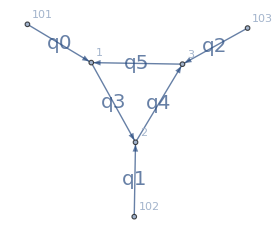

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[103,3,2],
DirectedEdge[1,2,3],
DirectedEdge[2,3,4],
DirectedEdge[3,1,5]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|3->0,4->0,5->0|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
lmbVec=q[cFFGetLMBEdges[Tri1L]⟦1⟧/.{DirectedEdge[_,_,props_]:>props["id"]}];
```

```mathematica
Dataset[GenerateLMBData[Tri1L,loopshift->{}]]
```

```mathematica
lmbData=GenerateLMBData[Tri1L,loopshift->{}];
lmbDataLambda=Association[Table[k-><|
"mass"->λ lmbData[k]["mass"],"lmb_decomposition"->Simplify[λ (lmbData[k]["lmb_decomposition"]/.{lmbVec->1/λ lmbVec})]|>,
{k,Keys[lmbData]}]]
```

<|0→<|mass→0,lmb_decomposition→λ q[0]|>,1→<|mass→0,lmb_decomposition→λ q[1]|>,2→<|mass→0,lmb_decomposition→λ q[2]|>,3→<|mass→0,lmb_decomposition→q[3]|>,4→<|mass→0,lmb_decomposition→-λ (q[0]+q[2])+q[3]|>,5→<|mass→0,lmb_decomposition→-λ q[0]+q[3]|>|>

```mathematica
ps=GetKinematics[-1/2,-3/4,-2/5];
N[ps,16]
Total[ps]
(ps[[1]]⟦1⟧)^2-(ps[[1]]⟦2⟧)^2-(ps[[1]]⟦3⟧)^2-(ps[[1]]⟦4⟧)^2
(ps[[2]]⟦1⟧)^2-(ps[[2]]⟦2⟧)^2-(ps[[2]]⟦3⟧)^2-(ps[[2]]⟦4⟧)^2
(ps[[3]]⟦1⟧)^2-(ps[[3]]⟦2⟧)^2-(ps[[3]]⟦3⟧)^2-(ps[[3]]⟦4⟧)^2
```

{{0,0.6970921746799343,0,-0.1185854122563142},{0,-0.6970921746799343,0,-0.5138701197773616},{0,0,0,0.6324555320336759}}

{0,0,0,0}

-1/2

-3/4

-2/5

```mathematica
Tri1LnumericsParametric={
k1->{kx,ky,kz},
p1->ps⟦1⟧[[2;;]],p2->ps⟦2⟧[[2;;]],p3->ps⟦3⟧[[2;;]],
p1E->ps⟦1⟧[[1]],p2E->ps⟦2⟧[[1]],p3E->ps⟦3⟧[[1]]
};
```

```mathematica
(*
Simplify[
ComputeSubtractionTermFromNormalized[
<|
"cFFexpr"->CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],
"num"->1,
"graph"->Tri1L
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><|2->1|>
|>,
Tri1Lnumerics(*{}*)][{-1,-1,1}]
]
*)
```

```mathematica
Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]]
```

-1/(4 √(kx^2+ky^2+kz^2) √((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2) √((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)))-1/(4 √(kx^2+ky^2+kz^2) √((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2) √((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)) (√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)))-1/(4 √(kx^2+ky^2+kz^2) √((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2) √((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)) (√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)))

```mathematica
MyIntegrand
```

-((8000 (2 √10 √(kx^2+ky^2+kz^2)+√(30-√3110 kx+40 kx^2+40 ky^2-13 √10 kz+40 kz^2)+√(20-√3110 kx+40 kx^2+40 ky^2+3 √10 kz+40 kz^2)))/(√(kx^2+ky^2+kz^2) √(30-√3110 kx+40 kx^2+40 ky^2-13 √10 kz+40 kz^2) √(20-√3110 kx+40 kx^2+40 ky^2+3 √10 kz+40 kz^2) (20 √(kx^2+ky^2+kz^2)+√10 √(30-√3110 kx+40 kx^2+40 ky^2-13 √10 kz+40 kz^2)) (√(30-√3110 kx+40 kx^2+40 ky^2-13 √10 kz+40 kz^2)+√(20-√3110 kx+40 kx^2+40 ky^2+3 √10 kz+40 kz^2)) (20 √(kx^2+ky^2+kz^2)+√10 √(20-√3110 kx+40 kx^2+40 ky^2+3 √10 kz+40 kz^2))))

```mathematica
ps=GetKinematics[-1/2,-3/4,-2/5];
Tri1LnumericsParametric={
k1->{kx,ky,kz},
p1->ps⟦1⟧[[2;;]],p2->ps⟦2⟧[[2;;]],p3->ps⟦3⟧[[2;;]],
p1E->ps⟦1⟧[[1]],p2E->ps⟦2⟧[[1]],p3E->ps⟦3⟧[[1]]
};
MyIntegrand=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]]//Simplify;
ClearAll[Integrand]
Integrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ]:=Module[
{param},
param=SphericalMap[x1,x2,x3];
param["jacobian"]*(MyIntegrand/.{
kx->param["vector"]⟦1⟧,
ky->param["vector"]⟦2⟧,
kz->param["vector"]⟦3⟧
})
]
MonitoredNIntegrate[
{
Integrand[x1,x2,x3]
,{x1,0,1},{x2,0,1},{x3,0,1}
,Method->"GlobalAdaptive",AccuracyGoal->15,PrecisionGoal->15,MaxPoints->10^5,MaxRecursion->20
},
TargetRes->N[π/2(-4.3693377349606655)],StackPrints->True,MonitorInterval->1.,Silence->True
]
%⟦1⟧//FullForm
```

0.   s : 0.K evals      ( 0.% )        -12.660919849389424  +- 17.7            ( 139.949% )   vs target 84.472%   ( 0.3σ )

1.   s : 15.4K evals    ( 15.4% )      -6.861135676524448   +- 0.000889        ( 0.013% )     vs target 0.032%    ( 2.5σ )

2.   s : 30.6K evals    ( 30.6% )      -6.86318577360902    +- 0.0002          ( 0.003% )     vs target 0.002%    ( 0.8σ )

3.   s : 46.K evals     ( 46.% )       -6.863066851278882   +- 0.0000788       ( 0.001% )     vs target 0.004%    ( 3.5σ )

4.   s : 61.6K evals    ( 61.6% )      -6.863173576698227   +- 0.0000442       ( 0.001% )     vs target 0.002%    ( 3.7σ )

5.   s : 77.1K evals    ( 77.1% )      -6.863277327845682   +- 0.0000256       ( 0.% )        vs target 0.001%    ( 2.4σ )

6.   s : 92.5K evals    ( 92.5% )      -6.86329158848904    +- 0.0000162       ( 0.% )        vs target 0.001%    ( 3.σ )

{-6.8633,}

-6.8633

Physical requires threshold subtraction of course

```mathematica
GetKinematics[1/4,2/3,2]
```

{{-19/(24 √2),0,0,-(√(73/2))/24},{-29/(24 √2),0,0,(√(73/2))/24},{√2,0,0,0}}

```mathematica
ps=GetKinematics[1/4,2/3,2];
Tri1LnumericsParametric={
k1->{kx,ky,kz},
p1->ps⟦1⟧[[2;;]],p2->ps⟦2⟧[[2;;]],p3->ps⟦3⟧[[2;;]],
p1E->ps⟦1⟧[[1]],p2E->ps⟦2⟧[[1]],p3E->ps⟦3⟧[[1]]
};
MyIntegrand=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]]//Simplify;
ClearAll[Integrand]
Integrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ]:=Module[
{param},
param=SphericalMap[x1,x2,x3];
param["jacobian"]*(MyIntegrand/.{
kx->param["vector"]⟦1⟧,
ky->param["vector"]⟦2⟧,
kz->param["vector"]⟦3⟧
})
]
MonitoredNIntegrate[
{
Integrand[x1,x2,x3]
,{x1,0,1},{x2,0,1},{x3,0,1}
,Method->"GlobalAdaptive",AccuracyGoal->15,PrecisionGoal->15,MaxPoints->10^5,MaxRecursion->20
},
TargetRes->N[π/2(3.0576270184668695)],StackPrints->True,MonitorInterval->1.,Silence->True
]
%⟦1⟧//FullForm
```

0.   s : 0.K evals      ( 0.% )        19.551753523660874   +- 66.2            ( 338.904% )   vs target 307.081%  ( 0.2σ )

1.   s : 12.1K evals    ( 12.1% )      -49.97378458465824   +- 116.            ( 232.724% )   vs target 1140.49%  ( 0.5σ )

2.   s : 24.5K evals    ( 24.5% )      4.390549178677921    +- 1.97            ( 44.933% )    vs target 8.586%    ( 0.2σ )

3.   s : 36.9K evals    ( 36.9% )      6.132278549669413    +- 1.44            ( 23.639% )    vs target 27.678%   ( 0.9σ )

4.   s : 49.1K evals    ( 49.1% )      8.121869649162019    +- 1.27            ( 15.686% )    vs target 69.103%   ( 2.6σ )

5.   s : 61.3K evals    ( 61.3% )      4.559366409611217    +- 1.25            ( 27.634% )    vs target 5.071%    ( 0.2σ )

6.   s : 73.5K evals    ( 73.5% )      2.737994693210734    +- 1.07            ( 39.311% )    vs target 42.993%   ( 1.9σ )

7.   s : 85.5K evals    ( 85.5% )      -1.4947913606432701  +- 0.995           ( 66.585% )    vs target 131.123%  ( 6.3σ )

8.   s : 97.4K evals    ( 97.4% )      -1.0813539875396243  +- 0.931           ( 86.112% )    vs target 122.515%  ( 6.3σ )

{-1.02461,}

-1.02461

### Second example: numerator, no UV, physical and euclidean

```mathematica
result=C0Expand[LoopRefine[LoopIntegrate[p1.k,k,{k,0},{k+p1,0},{k-p2,0}]]]/.{p1.p2->1/2(p3.p3-p1.p1-p2.p2)}
```

1/2 Log[-µ^2/(p2.p2)]-1/2 Log[-µ^2/(p3.p3)]-1/2 p1.p1 (-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3]))

```mathematica
p1sq=-1/2;
p2sq=-3/4;
p3sq=-2/5;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]//FullForm
```

Complex[-1.40664,0.]

```mathematica
p1sq=1/4;
p2sq=2/3;
p3sq=2;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]//FullForm
```

Complex[0.167103,7.79651×10^-17]

```mathematica
(*
mysol=Solve[{
EE^2+p2z^2==SP22,
EE^2+p1z^2==SP11,
Sqrt[SP33]+p2z+p1z==0
},{EE,p1z,p2z}]
{{0,-EE,0,p1z},{0,EE,0,p2z},{0,0,0,Sqrt[SP33]}}/.mysol⟦1⟧//FullSimplify

mysol=Solve[{
p1E^2-pz^2==SP11,
p2E^2-pz^2==SP22,
Sqrt[SP33]+p1E+p2E==0
},{pz,p1E,p2E}]
{{p1E,0,0,pz},{p2E,0,0,-pz},{Sqrt[SP33],0,0,0}}/.mysol⟦1⟧//FullSimplify
*)
```

#### Numerical Implementation

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[103,3,2],
DirectedEdge[1,2,3],
DirectedEdge[2,3,4],
DirectedEdge[3,1,5]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|3->0,4->0,5->0|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

-Graphics-

```mathematica
Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->SP4[q[0],q[3]],
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]];
```

```mathematica
ps=GetKinematics[-1/2,-3/4,-2/5];
Tri1LnumericsParametric={
k1->{kx,ky,kz},
p1->ps⟦1⟧[[2;;]],p2->ps⟦2⟧[[2;;]],p3->ps⟦3⟧[[2;;]],
p1E->ps⟦1⟧[[1]],p2E->ps⟦2⟧[[1]],p3E->ps⟦3⟧[[1]]
};
MyIntegrand=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->SP4[q[0],q[3]],
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]]//Simplify;
ClearAll[Integrand]
Integrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ]:=Module[
{param},
param=SphericalMap[x1,x2,x3];
param["jacobian"]*(MyIntegrand/.{
kx->param["vector"]⟦1⟧,
ky->param["vector"]⟦2⟧,
kz->param["vector"]⟦3⟧
})
]
MonitoredNIntegrate[
{
Integrand[x1,x2,x3]
,{x1,0,1},{x2,0,1},{x3,0,1}
,Method->"GlobalAdaptive",AccuracyGoal->15,PrecisionGoal->15,MaxPoints->10^5,MaxRecursion->20
},
TargetRes->N[(-1)(* I GUESS HERE THE OVERALL SIGN DEPENDS ON THE CONVENTION PACKAGEX USES FOR THE SIGN OF THE EXTERNAL *)*π/2(-1.4066387634513537)],StackPrints->True,MonitorInterval->1.,Silence->True
]
%⟦1⟧//FullForm
```

0.   s : 0.K evals      ( 0.% )        7.191514265471849    +- 13.             ( 180.828% )   vs target 225.475%  ( 0.4σ )

1.   s : 15.2K evals    ( 15.2% )      2.1988056842406514   +- 0.000227        ( 0.01% )      vs target 0.486%    ( 47.1σ )

2.   s : 30.3K evals    ( 30.3% )      2.209392795191526    +- 0.0000808       ( 0.004% )     vs target 0.007%    ( 1.9σ )

3.   s : 45.1K evals    ( 45.1% )      2.2093907223758444   +- 0.0000341       ( 0.002% )     vs target 0.007%    ( 4.5σ )

4.   s : 60.1K evals    ( 60.1% )      2.2094462652754387   +- 0.0000194       ( 0.001% )     vs target 0.004%    ( 5.σ )

5.   s : 75.K evals     ( 75.% )       2.2094632970249983   +- 0.0000115       ( 0.001% )     vs target 0.004%    ( 6.9σ )

6.   s : 89.7K evals    ( 89.7% )      2.2095238496627307   +- 8.77e-6         ( 0.% )        vs target 0.001%    ( 2.2σ )

{2.20953,}

2.20953

### Third example: numerator, UV, physical and euclidean

```mathematica
result=C0Expand[LoopRefine[LoopIntegrate[p1.k p2.k,k,{k,0},{k+p1,0},{k+p2,0}]]]
```

(p1.p2)/2+(p1.p2)/(4 ϵ)-1/4 p1.p1 Log[-µ^2/(p1.p1)]-1/4 p2.p2 Log[-µ^2/(p2.p2)]+1/4 (p1.p1+p1.p2+p2.p2) Log[-µ^2/(p1.p1-2 p1.p2+p2.p2)]+1/4 p1.p1 p2.p2 (-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)/(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)/(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]-2 p1.p2+2 p2.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]-2 p1.p2+2 p2.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]-2 p1.p2+2 p2.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2-2 p2.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]))

The diagram has a UV pole. We can construct a counter-term:

```mathematica
counterterm=LoopRefine[LoopIntegrate[p1.k p2.k,k,{k,muv},{k,muv},{k,muv}]]
```

1/4 p1.p2 (1/ϵ+Log[µ^2])

The diagram minus the counter-term evaluates to a finite quantity now:

```mathematica
subtractedresult=result-counterterm/.{p1.p2->-1/2(p3.p3-p1.p1-p2.p2)}//Simplify
```

1/8 (-p2.p2 (-2+Log[µ^2]+2 Log[-µ^2/(p2.p2)]-3 Log[-µ^2/(p3.p3)])+p3.p3 (-2+Log[µ^2]-Log[-µ^2/(p3.p3)])+p1.p1 (2-Log[µ^2]-2 Log[-µ^2/(p1.p1)]+3 Log[-µ^2/(p3.p3)]-1/(√Kallenλ[p1.p1,p2.p2,p3.p3])2 p2.p2 (PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]-PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]+PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]-PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]+PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)]-PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2-p3.p3)])))

```mathematica
p1sq=-1/2;
p2sq=-3/4;
p3sq=-2/5;
muv=1;
```

```mathematica
Assuming[ µ>0,subtractedresult/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]//FullForm
```

Complex[-0.865238,0.]

```mathematica
p1sq=1/4;
p2sq=2/3;
p3sq=1;
```

```mathematica
Assuming[ µ>0,subtractedresult/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]//FullForm
```

Complex[0.0921444,0.0327249]

#### Numerical Implementation

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[103,3,2],
DirectedEdge[1,2,3],
DirectedEdge[2,3,4],
DirectedEdge[3,1,5]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|3->0,4->0,5->0|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

-Graphics-

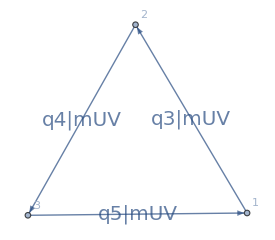

```mathematica
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,3],
DirectedEdge[2,3,4],
DirectedEdge[3,1,5]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|3->mUV,4->mUV,5->mUV|>,lmb->{3}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]]
```

```mathematica
Dataset[GenerateLMBData[Tri1L,loopshift->{}]]
```

```mathematica
origI=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->SP4[q[0],q[3]]*(SP4[q[1],q[5]]+SP4[q[1],q[0]]),
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]]
```

-(-17/40 (1/8 √(311/10) kx-(3 kz)/(8 √10))+(1/8 √(311/10) kx-(3 kz)/(8 √10)) (-1/8 √(311/10) (-(√(311/10))/8+kx)-(13 (3/(8 √10)+kz))/(8 √10)))/(4 √(kx^2+ky^2+kz^2) √((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2) √((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)))-(-17/40 (1/8 √(311/10) kx-(3 kz)/(8 √10))+(1/8 √(311/10) kx-(3 kz)/(8 √10)) (-1/8 √(311/10) (-(√(311/10))/8+kx)-(13 (3/(8 √10)+kz))/(8 √10)))/(4 √(kx^2+ky^2+kz^2) √((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2) √((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)) (√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)))-(-17/40 (1/8 √(311/10) kx-(3 kz)/(8 √10))+(1/8 √(311/10) kx-(3 kz)/(8 √10)) (-1/8 √(311/10) (-(√(311/10))/8+kx)-(13 (3/(8 √10)+kz))/(8 √10)))/(4 √(kx^2+ky^2+kz^2) √((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2) √((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2) (√(kx^2+ky^2+kz^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)) (√((-(√(311/10))/8+kx)^2+ky^2+(3/(8 √10)+kz)^2)+√((-(√(311/10))/8+kx)^2+ky^2+(-√(2/5)+3/(8 √10)+kz)^2)))

```mathematica
UVExternalsDefinition=Block[
{
externalEdges,externalEdgesIDs,momLabels,signatures
},
externalEdges=cFFGetExternalEdges[Tri1L];
externalEdgesIDs=Table[Evaluate[(ee/.{DirectedEdge[_,_,props_]:>props})]["id"],{ee,externalEdges}];
momLabels=cFFGenerateMomentaLabels[Tri1L];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Tri1L]}]];

Join[
(*Table[
q[eeID]->(signatures[eeID][[1]] . momLabels[[1]]+signatures[eeID][[2]] . momLabels[[2]])
,{eeID,externalEdgesIDs}],*)
Table[
q[externalEdgesIDs⟦ieeID⟧]->p[ieeID]
,{ieeID,Length[externalEdgesIDs]}],
Table[
qE[externalEdgesIDs⟦ieeID⟧]->ToExpression["p"<>ToString[ieeID]<>"E"]
,{ieeID,Length[externalEdgesIDs]}]
]
]
```

{q[0]→p[1],q[1]→p[2],q[2]→p[3],qE[0]→p1E,qE[1]→p2E,qE[2]→p3E}

```mathematica
subtractionNumerics=Join[
Tri1LnumericsParametric,
{mUV->10,
p[1][0]->(p1E/.Tri1Lnumerics),p[2][0]->(p2E/.Tri1Lnumerics),p[3][0]->(p3E/.Tri1Lnumerics),
p[1]->(p1/.Tri1Lnumerics),p[2]->(p2/.Tri1Lnumerics),p[3]->(p3/.Tri1Lnumerics)
}];
```

```mathematica
subtrI=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],Tri1LUVTopology],
"num"->(SP4[q[0],q[3]]*(SP4[q[1],q[5]]))/.UVExternalsDefinition,
"graph"->Tri1LUVTopology,
"dots"-><||>
|>,
subtractionNumerics,
UVRescaling->False
]]]
```

-(3 (-1/8 √(311/10) kx+(3 kz)/(8 √10)) (1/8 √(311/10) kx+(13 kz)/(8 √10)))/(16 (100+kx^2+ky^2+kz^2)^(5/2))

```mathematica
(*
N[(subtrI/.{kx->1r,ky->2r,kz->3r})/.{r->1000000},16]
N[(origI/.{kx->1r,ky->2r,kz->3r})/.{r->1000000},16]
N[((origI-1subtrI)/.{kx->1r,ky->2r,kz->3r})/.{r->1000000},16]
N[(subtrI/.{kx->1r,ky->2r,kz->3r})/.{r->10000000},16]
N[(origI/.{kx->1r,ky->2r,kz->3r})/.{r->10000000},16]
N[((origI-1subtrI)/.{kx->1r,ky->2r,kz->3r})/.{r->10000000},16]
*)
```

```mathematica
ps=GetKinematics[-1/2,-3/4,-2/5];
Tri1LnumericsParametric={
k1->{kx,ky,kz},
p1->ps⟦1⟧[[2;;]],p2->ps⟦2⟧[[2;;]],p3->ps⟦3⟧[[2;;]],
p1E->ps⟦1⟧[[1]],p2E->ps⟦2⟧[[1]],p3E->ps⟦3⟧[[1]]
};
subtractionNumerics=Join[
Tri1LnumericsParametric,
{mUV->1,
p[1][0]->(p1E/.Tri1LnumericsParametric),p[2][0]->(p2E/.Tri1LnumericsParametric),p[3][0]->(p3E/.Tri1LnumericsParametric),
p[1]->(p1/.Tri1LnumericsParametric),p[2]->(p2/.Tri1LnumericsParametric),p[3]->(p3/.Tri1LnumericsParametric)
}];
MyIntegrand=(
Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->SP4[q[0],q[3]]*(SP4[q[1],q[5]]+SP4[q[1],q[0]]),
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1LnumericsParametric,
UVRescaling->False
]]]
- Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],Tri1LUVTopology],
"num"->(SP4[q[0],q[3]]*(SP4[q[1],q[5]]))/.UVExternalsDefinition,
"graph"->Tri1LUVTopology,
"dots"-><||>
|>,
subtractionNumerics,
UVRescaling->False
]]]

)//Simplify;
ClearAll[Integrand]
Integrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ]:=Module[
{param},
param=SphericalMap[x1,x2,x3];
param["jacobian"]*(MyIntegrand/.{
kx->param["vector"]⟦1⟧,
ky->param["vector"]⟦2⟧,
kz->param["vector"]⟦3⟧
})
]
MonitoredNIntegrate[
{
Integrand[x1,x2,x3]
,{x1,0,1},{x2,0,1},{x3,0,1}
,Method->"AdaptiveMonteCarlo",AccuracyGoal->15,PrecisionGoal->15,MaxPoints->10^5,MaxRecursion->20
},
TargetRes->N[(-1)(* IN THIS CASE THERE ARE TWO EXTERNAL BUT SOMEHOW THE OVERALL SIGN IS STILL -1, MAYBE ONLY ONE OF THE EXTERNAL IS MEANT TO BE FLIPPED? *)*π/2(-0.8652383704701629)],StackPrints->True,MonitorInterval->1.,Silence->True
]
%⟦1⟧//FullForm
```

0.   s : 0.1K evals     ( 0.1% )       1.4034759377774264   +- 0.623           ( 44.414% )    vs target 3.264%    ( 0.1σ )

1.   s : 8.5K evals     ( 8.5% )       1.3625830956191385   +- 0.034           ( 2.497% )     vs target 0.255%    ( 0.1σ )

2.   s : 16.9K evals    ( 16.9% )      1.3285163413734662   +- 0.0164          ( 1.24% )      vs target 2.251%    ( 1.9σ )

3.   s : 25.5K evals    ( 25.5% )      1.3437526605618362   +- 0.0119          ( 0.887% )     vs target 1.13%     ( 1.3σ )

4.   s : 34.3K evals    ( 34.3% )      1.34368162280757     +- 0.00942         ( 0.701% )     vs target 1.135%    ( 1.6σ )

5.   s : 42.9K evals    ( 42.9% )      1.3511481260317786   +- 0.00755         ( 0.559% )     vs target 0.586%    ( 1.1σ )

6.1  s : 51.3K evals    ( 51.3% )      1.3529413453942594   +- 0.00646         ( 0.478% )     vs target 0.454%    ( 1.σ )

7.1  s : 59.9K evals    ( 59.9% )      1.3554263519589838   +- 0.00562         ( 0.415% )     vs target 0.271%    ( 0.7σ )

8.1  s : 68.7K evals    ( 68.7% )      1.353963448731198    +- 0.00492         ( 0.364% )     vs target 0.379%    ( 1.σ )

9.1  s : 77.3K evals    ( 77.3% )      1.3542990014062775   +- 0.00438         ( 0.324% )     vs target 0.354%    ( 1.1σ )

10.1 s : 85.9K evals    ( 85.9% )      1.3577318800488907   +- 0.00396         ( 0.292% )     vs target 0.102%    ( 0.3σ )

11.1 s : 94.5K evals    ( 94.5% )      1.3564311203617065   +- 0.0036          ( 0.265% )     vs target 0.197%    ( 0.7σ )

{1.35405,}

1.35405

## Boxes

The second set of benchmarks concerns the box diagram with vanishing internal masses, varying external masses and varying numerator. With this setup, the box diagram is a function of six invariants. Contrary to the triangle, we now derive the invariants from explicit values of four-momenta for the external particles, for ease of execution. The diagram reads

We can now test IR and UV subtraction and the correct implementation of numerators in the euclidean and physical regime.

### Finite boxes in physical region

We start with finite boxes. While for the triangle there is always a frame in which all E-surfaces admit a single center, this is not the case for the boxes. We should a challenging physical point with multiple overlaps, for example:

```mathematica
p1phys={0.99,0,0.96,0};
p2phys={0.82,0.65,0.,0};
p4phys={-0.71,-0.45,-0.53,0};
p3phys=-p1phys-p2phys-p4phys;
```

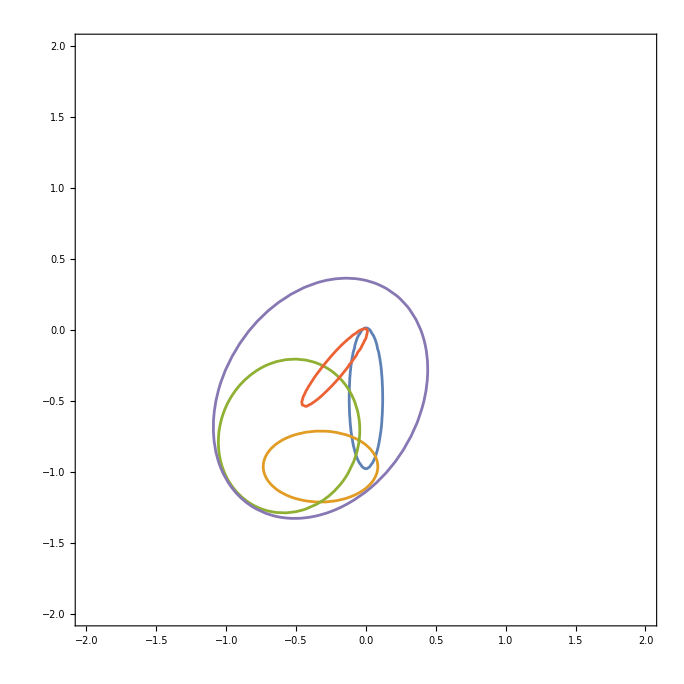

```mathematica
ContourPlot[{esurf[{kx,ky,0},zerovec,p1phys]==0,esurf[{kx,ky,0},p1phys,p1phys+p2phys]==0,esurf[{kx,ky,0},p1phys+p2phys+p3phys,p1phys+p2phys]==0,esurf[{kx,ky,0},p1phys+p2phys+p3phys+p4phys,p1phys+p2phys+p3phys]==0,esurf[{kx,ky,0},zerovec,p1phys+p2phys]==0,esurf[{kx,ky,0},p1phys,p1phys+p2phys+p3phys]==0},{kx,-2,2},{ky,-2,2}]
```

#### First example: no numerator

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]]]
```

ConditionalExpression[ScalarC0[p2.p2 p4.p4,(p1.p1+2 p1.p2+p2.p2) (p1.p1+2 p1.p4+p4.p4),p1.p1 (p1.p1+2 p1.p2+2 p1.p4+p2.p2+2 p2.p4+p4.p4),0,0,0], ]

```mathematica
p1sq=SP[p1phys,p1phys];
p2sq=SP[p2phys,p2phys];
p4sq=SP[p4phys,p4phys];
p1p4=SP[p1phys,p4phys];
p1p2=SP[p1phys,p2phys];
p2p4=SP[p2phys,p4phys];
```

```mathematica
C0Expand[result/.{p1.p1->p1sq,p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}]
```

-7.93527-34.7353 ⅈ

#### Second example: numerator

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[k.p1 k.p2 k.p4,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]]];
```

```mathematica
p1sq=SP[p1phys,p1phys];
p2sq=SP[p2phys,p2phys];
p4sq=SP[p4phys,p4phys];
p1p4=SP[p1phys,p4phys];
p1p2=SP[p1phys,p2phys];
p2p4=SP[p2phys,p4phys];
```

```mathematica
Assuming[ µ>0,C0Expand[result/.{p1.p1->p1sq,p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}]//PowerExpand//Simplify//N]
```

(0.467305-0.361178 ⅈ)-8.32667×10^-17 Log[µ]

### Divergent boxes

We need to cook up a bunch of IR-singular momentum configurations for the external legs.

1) Euclidean, one massless external:

```mathematica
p1unphys1os={1,0,1,0};
p2unphys1os={-0.2,0.65,0.,0};
p4unphys1os={-0.71,-0.45,-0.53,-0.4};
p3unphys1os=-p1unphys1os-p2unphys1os-p4unphys1os;
```

```mathematica
{SP[p1unphys1os,p1unphys1os],
SP[p2unphys1os,p2unphys1os],
SP[p3unphys1os,p3unphys1os],
SP[p4unphys1os,p4unphys1os],
SP[p1unphys1os+p2unphys1os,p1unphys1os+p2unphys1os],
SP[p1unphys1os+p4unphys1os,p1unphys1os+p4unphys1os]}
```

{0,-0.3825,-0.4128,-0.1393,-0.7825,-0.4993}

2) Euclidean, two massless externals

```mathematica
p1unphys2os={1,0,1,0};
p2unphys2os={-1,1,0.,0};
p4unphys2os={-0.71,-0.45,-0.53,-0.4};
p3unphys2os=-p1unphys2os-p2unphys2os-p4unphys2os;
```

```mathematica
{SP[p1unphys2os,p1unphys2os],
SP[p2unphys2os,p2unphys2os],
SP[p3unphys2os,p3unphys2os],
SP[p4unphys2os,p4unphys2os],
SP[p1unphys2os+p2unphys2os,p1unphys2os+p2unphys2os],
SP[p1unphys2os+p4unphys2os,p1unphys2os+p4unphys2os]}
```

{0,0.,-0.1793,-0.1393,-2.,-0.4993}

3) Physical, one massless external

```mathematica
p1phys1os={1,0,1,0};
p2phys1os={0.82,0.45,0.,0};
p4phys1os={-0.71,-0.55,-0.23,0};
p3phys1os=-p1phys1os-p2phys1os-p4phys1os;
```

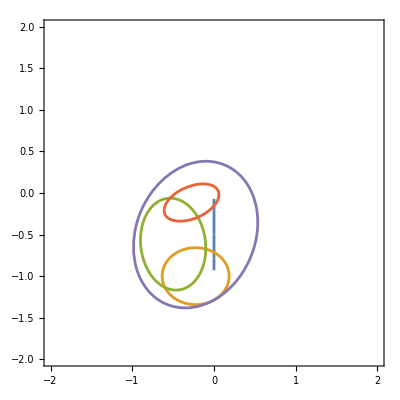

```mathematica
ContourPlot[{esurf[{kx,ky,0},zerovec,p1phys1os]==0,esurf[{kx,ky,0},p1phys1os,p1phys1os+p2phys1os]==0,esurf[{kx,ky,0},p1phys1os+p2phys1os+p3phys1os,p1phys1os+p2phys1os]==0,esurf[{kx,ky,0},p1phys1os+p2phys1os+p3phys1os+p4phys1os,p1phys1os+p2phys1os+p3phys1os]==0,esurf[{kx,ky,0},zerovec,p1phys1os+p2phys1os]==0,esurf[{kx,ky,0},p1phys1os,p1phys1os+p2phys1os+p3phys1os]==0},{kx,-2,2},{ky,-2,2}]
```

4) Physical, two massless externals

```mathematica
p1phys2os={1,0,1,0};
p2phys2os={1,0,-1,0};
p4phys2os={-0.71,-0.45,-0.53,0};
p3phys2os=-p1phys2os-p2phys2os-p4phys2os;
```

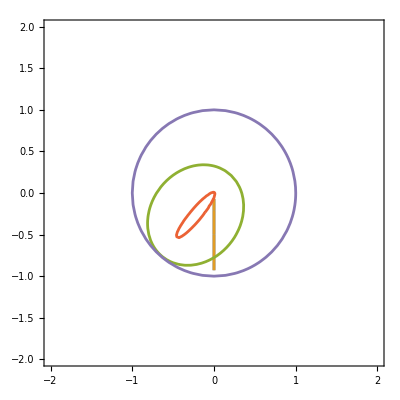

```mathematica
ContourPlot[{esurf[{kx,ky,0},zerovec,p1phys2os]==0,esurf[{kx,ky,0},p1phys2os,p1phys2os+p2phys2os]==0,esurf[{kx,ky,0},p1phys2os+p2phys2os+p3phys2os,p1phys2os+p2phys2os]==0,esurf[{kx,ky,0},p1phys2os+p2phys2os+p3phys2os+p4phys2os,p1phys2os+p2phys2os+p3phys2os]==0,esurf[{kx,ky,0},zerovec,p1phys2os+p2phys2os]==0,esurf[{kx,ky,0},p1phys2os,p1phys2os+p2phys2os+p3phys2os]==0},{kx,-2,2},{ky,-2,2}]
```

#### IR divergent box: no numerator

We start with case 1)

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0}]];
```

```mathematica
p2sq=SP[p2unphys1os,p2unphys1os];
p4sq=SP[p4unphys1os,p4unphys1os];
p1p4=SP[p1unphys1os,p4unphys1os];
p1p2=SP[p1unphys1os,p2unphys1os];
p2p4=SP[p2unphys1os,p4unphys1os];
```

```mathematica
resultBox1os=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-5.35039-5.90464/ϵ-11.8093 Log[µ]

This box has a collinear singularity, we need to subtract it. We follow the method laid out in [arXiv:1912.09291]. We construct the two triangle integrals obtained by contracting one-by-one the edges of the graph that are hard in the collinear limit:

```mathematica
ctTriangle1=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0}]];
ctTriangle2=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0}]/.{p1.p1->0}]];
```

and we take the linear combination of them that subtracts locally the singularity, which can be obtained by solving a simple linear system

```mathematica
((Collect[
CoefficientList[TensorExpand[(t1*(k-p4).(k-p4)+t2*(k+p1+p2).(k+p1+p2))]//.{LDot[k,a_]:>x*LDot[p1,a],LDot[a_,k]:>x*LDot[a,p1]}/.{p1.p1->0},x],{t1,t2}])
//MatrixForm)
```

(t2 (2 p1.p2+p2.p2)+t1 p4.p4
2 t2 p1.p2-2 t1 p1.p4)

```mathematica
sol=Solve[{2p1.p2 t2 -2 p1.p4 t1==0, t2(2p1.p2+p2.p2)+t1 p4.p4==1},{t1,t2}][[1]]
```

{t1→(p1.p2)/(2 p1.p2 p1.p4+p1.p4 p2.p2+p1.p2 p4.p4),t2→(p1.p4)/(2 p1.p2 p1.p4+p1.p4 p2.p2+p1.p2 p4.p4)}

```mathematica
ctBox1os=C0Expand[(t1 ctTriangle1+t2 ctTriangle2)/.sol];
cteval=Assuming[ µ>0,ctBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-6.32203-5.90464/ϵ-11.8093 Log[µ]

Now the difference between the original integral and the counter-term is finite:

```mathematica
subtractedBox1os=resultBox1os-ctBox1os;
```

```mathematica
subtractedresult=resulteval-cteval//Simplify
```

0.97164+1.77636×10^-15 Log[µ]

We now proceed with case 2)

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
p4sq=SP[p4unphys2os,p4unphys2os];
p1p4=SP[p1unphys2os,p4unphys2os];
p1p2=SP[p1unphys2os,p2unphys2os];
p2p4=SP[p2unphys2os,p4unphys2os];
```

```mathematica
resultBox2os=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-2.45779+1.0014/ϵ^2-2.99807/ϵ+(-5.99614+2.0028/ϵ) Log[µ]+2.0028 Log[µ]^2

Since the box has now two adjacent massless externals, there is now a soft singularity, identified by a double pole. The counter-term is constructed in the same way as before:

```mathematica
ctTriangle1=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
ctTriangle2=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0}]/.{p1.p1->0,p2.p2->0}]];
ctTriangle3=C0Expand[LoopRefine[LoopIntegrate[1,k,{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
sol=Solve[{2p1.p2 t2 -2 p1.p4 t1==0, 1-t2(2p1.p2)-t1 p4.p4==0,t1==1/(2p1.p4+p4.p4), t1(p1.p2+p2.p4)+t3 p1.p2==0},{t1,t2,t3}][[1]]
```

{t1→-1/(-2 p1.p4-p4.p4),t2→(p1.p4)/(p1.p2 (2 p1.p4+p4.p4)),t3→-(p1.p2+p2.p4)/(p1.p2 (2 p1.p4+p4.p4))}

```mathematica
ctBox2os=C0Expand[(t1 ctTriangle1+t2 ctTriangle2+t3 ctTriangle3)/.sol];
```

```mathematica
cteval=Assuming[ µ>0,ctBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-3.5244+1.0014/ϵ^2-2.99807/ϵ+(-5.99614+2.0028/ϵ) Log[µ]+2.0028 Log[µ]^2

Now the difference is finite

```mathematica
subtractedBox2os=resultBox2os-ctBox2os;
```

```mathematica
subtractedresult=resulteval-cteval//Simplify
```

1.06661-1.33227×10^-15 Log[µ]^2

We can re-use the subtracted boxes we derived to immediately obtain the value at physical points, 3) and 4):

```mathematica
p2sq=SP[p2phys1os,p2phys1os];
p4sq=SP[p4phys1os,p4phys1os];
p1p4=SP[p1phys1os,p4phys1os];
p1p2=SP[p1phys1os,p2phys1os];
p2p4=SP[p2phys1os,p4phys1os];
```

```mathematica
Assuming[ µ>0,resultBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-1.64086+1.67947 ⅈ)+(1.79531+1.76332 ⅈ)/ϵ+(3.59061+3.52664 ⅈ) Log[µ]

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(0.11827-4.32939 ⅈ)-(0.+4.44089×10^-16 ⅈ)/ϵ-(0.+8.88178×10^-16 ⅈ) Log[µ]-2.22045×10^-16 Log[µ]^2

```mathematica
p4sq=SP[p4phys2os,p4phys2os];
p1p4=SP[p1phys2os,p4phys2os];
p1p2=SP[p1phys2os,p2phys2os];
p2p4=SP[p2phys2os,p4phys2os];
```

```mathematica
Assuming[ µ>0,resultBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-0.970603+7.59491 ⅈ)-0.736811/ϵ^2+(2.16333+2.31476 ⅈ)/ϵ+((4.32665+4.62952 ⅈ)-1.47362/ϵ) Log[µ]-1.47362 Log[µ]^2

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-1.92127-4.20529 ⅈ)+(4.44089×10^-16+0. ⅈ)/ϵ-(3.07819×10^-16-6.97574×10^-16 ⅈ) Log[µ]+6.66134×10^-16 Log[µ]^2

#### IR divergent boxes: numerator

We start with the point 1):

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[p4.k,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0}]];
```

```mathematica
p2sq=SP[p2unphys1os,p2unphys1os];
p4sq=SP[p4unphys1os,p4unphys1os];
p1p4=SP[p1unphys1os,p4unphys1os];
p1p2=SP[p1unphys1os,p2unphys1os];
p2p4=SP[p2unphys1os,p4unphys1os];
```

```mathematica
resultBox1osNum=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-2.89532+0. ⅈ)-0.483449/ϵ-0.966897 Log[µ]-3.33067×10^-16 Log[µ]^2

The counter-term is:

```mathematica
ctBox1osNum=1/2(p4.p4)ctBox1os-1/2D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0}]];
```

```mathematica
cteval=Assuming[ µ>0,ctBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-0.0993077-0.483449/ϵ-0.966897 Log[µ]

and the subtracted integrand is finite:

```mathematica
subtractedBox1osNum=resultBox1osNum-ctBox1osNum;
```

```mathematica
Assuming[ µ>0,subtractedBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-2.79601+0. ⅈ)-(5.55112×10^-17)/ϵ+2.22045×10^-16 Log[µ]-1.11022×10^-16 Log[µ]^2

We may now proceed to point 2):

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[p4.k,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
p4sq=SP[p4unphys2os,p4unphys2os];
p1p4=SP[p1unphys2os,p4unphys2os];
p1p2=SP[p1unphys2os,p2unphys2os];
p2p4=SP[p2unphys2os,p4unphys2os];
```

```mathematica
resultBox2osNum=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox2osNum/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

1.9565+0.180252/ϵ^2+1.63576/ϵ+(3.27152+0.360505/ϵ) Log[µ]+0.360505 Log[µ]^2

The counter-term is now given by

```mathematica
ctBox2osNum=1/2(p4.p4)ctBox2os-1/2D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]]+1/2D0Expand[LoopRefine[LoopIntegrate[1,k,{k+p1,0},{k+p1+p2,0},{k-p4,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
cteval=Assuming[ µ>0,ctBox2osNum/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

2.03079+0.180252/ϵ^2+1.63576/ϵ+(3.27152+0.360505/ϵ) Log[µ]+0.360505 Log[µ]^2

and the subtracted integrand is finite:

```mathematica
subtractedBox2osNum=resultBox2osNum-ctBox2osNum;
```

```mathematica
Assuming[ µ>0,subtractedBox2osNum/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-0.0742893-(1.38778×10^-17)/ϵ^2-(4.16334×10^-16)/ϵ+(-4.44089×10^-16-(2.22045×10^-16)/ϵ) Log[µ]-2.22045×10^-16 Log[µ]^2

We can straight-forwardly replicate the calculation for the physical points, 3) and 4):

```mathematica
p2sq=SP[p2phys1os,p2phys1os];
p4sq=SP[p4phys1os,p4phys1os];
p1p4=SP[p1phys1os,p4phys1os];
p1p2=SP[p1phys1os,p2phys1os];
p2p4=SP[p2phys1os,p4phys1os];
```

```mathematica
Assuming[ µ>0,resultBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(1.12253-0.76375 ⅈ)+(0.59137+0.131103 ⅈ)/ϵ+(1.18274+0.262206 ⅈ) Log[µ]-2.77556×10^-17 Log[µ]^2

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(1.25136-2.64901 ⅈ)+(0.+8.32667×10^-17 ⅈ)/ϵ-(0.+1.66533×10^-16 ⅈ) Log[µ]-8.32667×10^-17 Log[µ]^2

```mathematica
p4sq=SP[p4phys2os,p4phys2os];
p1p4=SP[p1phys2os,p4phys2os];
p1p2=SP[p1phys2os,p2phys2os];
p2p4=SP[p2phys2os,p4phys2os];
```

```mathematica
Assuming[ µ>0,resultBox2osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-1.2214+0.451345 ⅈ)-0.132626/ϵ^2-(0.214513-0.664677 ⅈ)/ϵ+((-0.429026+1.32935 ⅈ)-0.265252/ϵ) Log[µ]-0.265252 Log[µ]^2

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox2osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-0.0198852-0.0435248 ⅈ)-(5.20417×10^-18)/ϵ^2+(4.33681×10^-17+2.22045×10^-16 ⅈ)/ϵ+((0.+4.44089×10^-16 ⅈ)+(5.55112×10^-17)/ϵ) Log[µ]